{1.98881,0.0000531326}

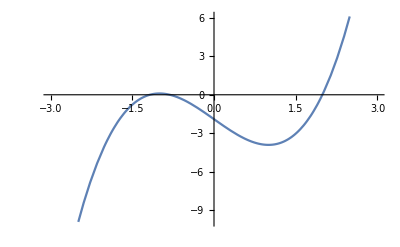

```mathematica
f[x_]:=x^3-3x+4-5.9
e=1*10^-4;a=1*10^-10;
b=20;
isRoot=False;
While[isRoot==False,
x=(a+b)/2;
(*Print[x," ",f[x]];*)
isRoot = Abs[f[x]]≤e;
If[f[a]f[x]<0,
b=x, 
a=x]
]
N[{x,f[x]}]
Plot[f[x], {x, -3, 3}]
```